```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/niels/Projects/Johannes

```mathematica
ℏc=197.32858;
Mnucl=(938.2796+939.5731)/2.;
multiplicity=1;
parity="-";
J=0.5;
k=20;
```

```mathematica
NormHamMat=ReadList["norm-ham-litME-"<>ToString[J]<>"^"<>parity,Number];
JbasisDim=NormHamMat[[1]];
```

```mathematica
norm=ArrayReshape[NormHamMat[[2;;JbasisDim^2+1]],{JbasisDim,JbasisDim}];ham=ArrayReshape[NormHamMat[[JbasisDim^2+2;;2 JbasisDim^2+1]],{JbasisDim,JbasisDim}];
```

```mathematica
file="LIT_SOURCE_"<>ToString[J]<>"^"<>parity<>"_mJ"<>ToString[J]<>"_MUL"<>ToString[multiplicity];
inhomo=ReadList[file,Real,RecordLists->True];
```

```mathematica
renorm=DiagonalMatrix[1/Sqrt[Diagonal[norm]]];
```

```mathematica
ham=renorm.ham.renorm;norm=renorm.norm.renorm;inhomo=renorm.#&/@inhomo;
```

```mathematica
Grid[{{"ev(⟨i|j⟩)\n","ev(⟨i|H_nucl|j⟩)","⟨i|E1(k)|He⟩"},{Eigenvalues[norm]//MatrixForm,Eigenvalues[{ham,norm}]//MatrixForm,inhomo[[k]]//MatrixForm}}]
```

ev(⟨i|j⟩)
 | ev(⟨i|H_nucl|j⟩) | ⟨i|E1(k)|He⟩
(15.3768
3.0165
1.17662
0.331971
0.085839
0.00901412
0.00258868
0.00041596
0.000221347
0.0000405314
0.0000191421
8.53342×10^-7
5.45318×10^-7
5.72152×10^-8
4.92269×10^-8
9.82733×10^-9
2.81845×10^-9
2.68272×10^-10
8.57254×10^-11
5.17522×10^-12) | (489.949
248.305
212.516
177.779
155.311
127.979
104.734
96.6955
90.7625
69.5494
60.1934
51.4194
44.6072
36.2831
30.1545
19.5285
17.4506
10.6678
5.49531
2.4226) | (0.
0.
0.
0.
0.
0.0176953
0.0230907
0.0132888
0.0146061
0.0112639
0.0377891
0.117417
0.00657813
0.01165
0.0152137
0.011809
0.00644655
0.00876731
0.0149611
0.00584149)

```mathematica
inhomo[[20]]=norm[[20,;;19]];
```

```mathematica
norm=norm[[;;19,;;19]];ham=ham[[;;19,;;19]];
```

## An unstable test case

What we are trying to solve: the operator equation (ℋ-σ ℐ)|ϕ⟩=|ψ⟩; σ=σ_R+ⅈ σ_I; the result (lit transform) is given by ℒ=⟨ϕ|ϕ⟩. We now decompose |ϕ⟩ and |ψ⟩  in the same nonorthogonal basis |i⟩.
Define N_ij=⟨i|j⟩, H_ij=⟨i|ℋ|j⟩, ψ_i=⟨i|ψ⟩, |ϕ⟩=ϕ_i|i⟩, i.e., ϕ_i=N_ij^-1⟨j|ϕ⟩.  Now solve the equation for ϕ,
(H_ij-σ N_ij)ϕ_i=ψ_i, and calculate ℒ=⟨ϕ|ϕ⟩=ϕ_i N_ij ϕ_j.

```mathematica
σI=5;
σRmin=-10.;σRmax=100.;σRstep=1;
σRs=Range[σRmin,σRmax,σRstep];
litOfSigma={};litOfSigmaNaive={};
psilitOfSigma={};psilitOfSigmaNaive={};
```

```mathematica
ltsσ=Function[{σR},(*{psilitOfSigmaNaive,litOfSigmaNaive,psilitOfSigma,litOfSigma}*)
Block[{coeff},{coeff=Inverse[ham-(σR-σI I) norm].inhomo[[k]];Conjugate[coeff].norm.coeff,coeff=LinearSolve[ham-Conjugate[σR+σI I] norm,inhomo[[k]]];Conjugate[coeff].norm.coeff}]
];
```

```mathematica
{litOfSigmaNaive,litOfSigma}=Transpose[ltsσ/@σRs];
```

Inverse::luc: Result for Inverse of badly conditioned matrix {{16.3885+5. ⅈ,9.57269+3.45438 ⅈ,10.886+2.68122 ⅈ,14.3959+3.81441 ⅈ,9.31517+2.2188 ⅈ,12.2288+3.09537 ⅈ,13.4434+3.48762 ⅈ,«5»,7.27998+1.64226 ⅈ,7.81885+1.79281 ⅈ,4.16788+0.795604 ⅈ,3.5025+0.616522 ⅈ,4.40365+0.859755 ⅈ,5.21409+1.07795 ⅈ,3.37065+0.580753 ⅈ},«17»,{3.37065+«1»,«18»}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{16.3885+5. ⅈ,9.57269+3.45438 ⅈ,10.886+2.68122 ⅈ,14.3959+3.81441 ⅈ,9.31517+2.2188 ⅈ,12.2288+3.09537 ⅈ,13.4434+3.48762 ⅈ,«5»,7.27998+1.64226 ⅈ,7.81885+1.79281 ⅈ,4.16788+0.795604 ⅈ,3.5025+0.616522 ⅈ,4.40365+0.859755 ⅈ,5.21409+1.07795 ⅈ,3.37065+0.580753 ⅈ},«17»,{3.37065+«1»,«18»}} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {«1»} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {«1»} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {«1»} may contain significant numerical errors.

General::stop: Further output of Inverse::luc will be suppressed during this calculation.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {«1»} may contain significant numerical errors.

General::stop: Further output of LinearSolve::luc will be suppressed during this calculation.

```mathematica
naive=ListPlot[{Re[litOfSigma],Re[litOfSigmaNaive]},AxesLabel->{"σ_real","a_j𝟙_jia_i ∝ Lit"},PlotLabels->{"mm function","naive"},ImageSize->Large,DataRange->{σRmin,σRmax},Joined->{True,False}]
```

-Graphics-

## A stabilization attempt via singular-value decomposition

### reduced-basis (Moore-Penrose pseudo inverse, vs SVD of eigensystem)

Here we tackle the full matrix. Disadvantage of that can be is a separate inverse for each σ; no communality between the truncations at different σ. 
This relies on a pseudo inverse

Use M_ij=(H_ij-σ N_ij).
Write the SVD M=U S A^† with S=diag and U=U^T and A=A^T (both orthogonal as M is square)
S_ii=√(ev_i(M^T M)). We can  now define a pseudo inverse by
M^-1=A P S^-1 P U^†, where P  projects on sensible values  of S (greater than a threshold t)

There is an alternative
(H_ij-σ N_ij)ϕ_i=ψ_i. Diagonalise N, N_ij O_jn=μ^(n)O_in, call the eigenvalues μ. Define (ϕ̃)_j=N_ji^(1/2)ϕ_i, where N_ji^x=O_bj μ_b^x O_bi^We then solve
(N_ki^(-1/2)H_ij N_lj^(-1/2)-σ )(ϕ̃)_l=N_li^(-1/2)ψ_i. Again, the subset of indices b is defined by a truncation, μ^(n)>t. The Lit is now ℒ=⟨ϕ|ϕ⟩=(ϕ̃)_l(ϕ̃)_l.
After ignoring the outer orthogonal transformations, that hide the basis reduction, this becomes even simpler in terms of the eigenvalues of (H̃)_ab=μ_a^(-1/2) O_ai H_ij O_bj μ_b^(-1/2); Writing (H̃)_ab e_b^(m)=λ^(m)e_a^(m), and (ψ̃)^(m)=∑_a e_a^(m)μ_a^(-1/2) O_ai ψ_i, we have ℒ=⟨ϕ|ϕ⟩=∑_m (|(ψ̃)^(m)|^2)/(|λ^(m)-σ|^2)

```mathematica
pseudoinverse[threshold_,σR_,σI_]:=Block[{Mm=ham-(σR-σI ⅈ) norm,USA,dimred},PseudoInverse[Mm,Tolerance->threshold]]
```

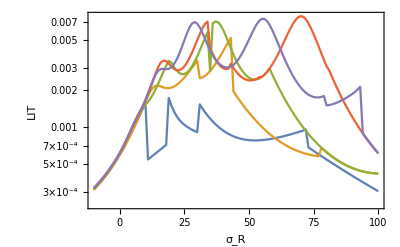

```mathematica
ListLogPlot[(Function[{σR},Block[{mm,coeff},mm=pseudoinverse[#,σR,σI];coeff=mm.inhomo[[k]];{σR,Chop[Conjugate[coeff].norm.coeff]}]]/@σRs)&/@{10^-1,10^-2,10^-3,10^-4,10^-5},PlotRange->All,Joined->True,Frame->True,FrameLabel->{"σ_R","LIT"}]
```

Here we see one of the potential problems of this approach: eigenvalues can slip through the tolerance as we change σ_R, changing the result drastically. That is a real worry!

#### Alternative approach (norm zero-mode removal)

```mathematica
Clear[normreg];normreg[threshold_]:=Block[{es=Eigensystem[norm],μ,transf,μs,Or},{μ,transf}=Transpose[Select[Sort[Transpose[es],#1[[1]]<#2[[1]]&],#[[1]]>threshold&]];{μs,Or}=Transpose[Select[Sort[Transpose[es],#1[[1]]<#2[[1]]&],#[[1]]<=threshold&]];{(Transpose[transf].DiagonalMatrix[μ^(-1/2)]),Or,μs}]
```

```mathematica
Clear[decompose];decompose[threshold_,k_,pr_:False,debug_:False]:= Block[{Oμ,Or,μs,oλs,otrf},{Oμ,Or,μs}=normreg[threshold];If[debug,Print[MatrixForm[Chop[(Transpose[Oμ].norm).Oμ]]]];{λs,trf}=Eigensystem[(Transpose[Oμ].ham).Oμ];If[pr,Print["overlap of ψ with norm zero modes (norm, overlap)\n",MatrixForm[Transpose[{μs,Or.inhomo[[k]]}]]]];{λs,trf.(Transpose[Oμ].inhomo[[k]])}]
```

```mathematica
litcomp[threshold_,k_:k]:=Block[{λscf=Transpose[decompose[threshold,k]]},Plus@@(((#[[2]])^2/((#[[1]]-σRe)^2+σIm^2))&/@λscf)]
```

```mathematica
litshow[threshold_,k_]:=Block[{λscf=Transpose[decompose[threshold,k]]},{#[[1]],Abs[#[[2]]]^2}&/@λscf]
```

```mathematica
decompose[10^-6,20,True]
```

overlap of ψ with norm zero modes (norm, overlap)
(4.03568×10^-11 | 5.50058×10^-10
1.18081×10^-10 | -7.23845×10^-10
5.80032×10^-10 | -3.29428×10^-9
4.31604×10^-9 | 7.20481×10^-9
3.69423×10^-8 | -4.03614×10^-8
5.52945×10^-8 | 1.13629×10^-8
3.39179×10^-7 | 4.21648×10^-7
7.49844×10^-7 | 2.8675×10^-7)

{{283.857,128.34,116.308,76.0655,58.1586,43.5418,27.8813,22.0555,13.6219,6.28561,2.48164},{-0.233992,0.209979,0.354605,-0.558815,0.0636623,0.545279,0.279603,-0.221831,-0.175855,0.0575492,-0.0114586}}

This exposes a problem, the r.h.s has non-zero components (or at least components much larger than √μ) in the direction of the zero modes. This means solution of the inversion problem is very unstable under change of the number of components, as we shall see below.

```mathematica
decompose[10^-4,k,True,True]
```

(1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.)

overlap of ψ with norm zero modes (norm, overlap)
(4.03568×10^-11 | 5.50058×10^-10
1.18081×10^-10 | -7.23845×10^-10
5.80032×10^-10 | -3.29428×10^-9
4.31604×10^-9 | 7.20481×10^-9
3.69423×10^-8 | -4.03614×10^-8
5.52945×10^-8 | 1.13629×10^-8
3.39179×10^-7 | 4.21648×10^-7
7.49844×10^-7 | 2.8675×10^-7
0.0000165966 | -9.27262×10^-6
0.0000367602 | -0.0000147506)

{{231.355,96.8697,89.8979,54.7699,36.5457,28.3371,14.9901,6.56346,2.50662},{0.308766,0.403802,0.373222,-0.602661,-0.110442,-0.426816,0.200089,-0.0677078,0.0105791}}

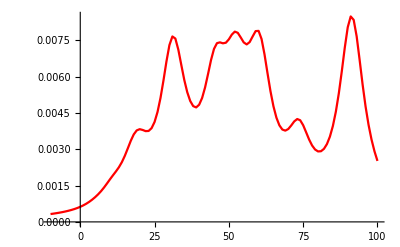

```mathematica
alt=ListLinePlot[Function[{σR},Block[{mm,coeff},mm=pseudoinverse[10^-18,σR,σI];coeff=mm.inhomo[[k]];{σR,Re[Conjugate[coeff].norm.coeff]}]]/@σRs,PlotRange->All,PlotStyle->Red]
```

```mathematica
Show[Plot[Evaluate[litcomp[10^-20]/.σIm->σI],{σRe,-10,100}],naive,alt]
```

Transpose::nmtx: The first two levels of If[If[False||False,False,{}=!=$BoxForms∩(FormatType/.List/@Options[$Messages∩Join[Streams[],{stdout,stderr}],FormatType])],System`Dump`TypesetCompact[{}],System`Dump`TextualCompact[{}]] cannot be transposed.

Set::shape: Lists If[If[False||False,False,{}=!=$BoxForms∩(FormatType/.List/@Options[$Messages∩Join[Streams[],{stdout,stderr}],FormatType])],System`Dump`TypesetCompact[{μs,Or}],System`Dump`TextualCompact[{μs,Or}]] and If[If[False||False,False,{}=!=$BoxForms∩(FormatType/.List/@Options[$Messages∩Join[Streams[],{stdout,stderr}],FormatType])],System`Dump`TypesetCompact[Transpose[{}]],System`Dump`TextualCompact[Transpose[{}]]] are not the same shape.

-Graphics-

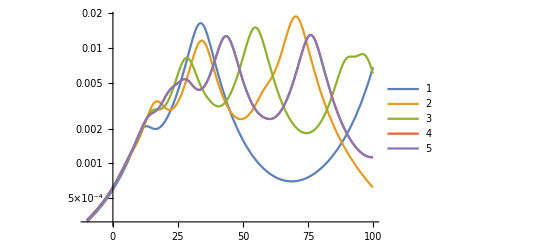

```mathematica
LogPlot[Evaluate[((f=litcomp[#]/.σIm->σI)&/@{0.1,0.001,0.0001,0.00001,0.000001})],{σRe,-10,100},PlotLegends->Automatic]
```

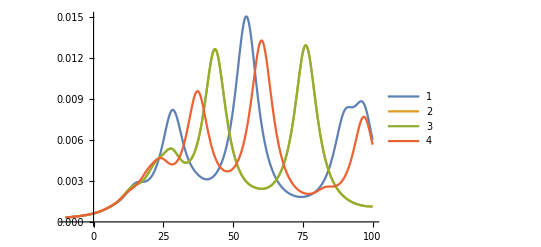

```mathematica
Plot[Evaluate[((f=litcomp[#]/.σIm->σI)&/@{10^-4,10^-5,10^-6,10^-7})],{σRe,-10,100},PlotLegends->Automatic]
```

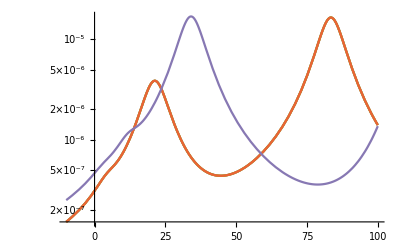

```mathematica
LogPlot[Evaluate[((f=litcomp[#]/.σIm->σI)&/@{1,0.8,0.6,0.4,0.2})],{σRe,-10,100},PlotRange->All]
```

```mathematica
inhomo[[k]].Inverse[norm].inhomo[[k]]
```

Inverse::luc: Result for Inverse of badly conditioned matrix {{1.,0.690877,0.536243,0.762882,0.443761,0.619075,0.697525,0.267957,0.402256,0.249365,0.301811,0.200523,0.328452,0.358562,0.159121,0.123304,0.171951,0.215591,0.116151},{0.690877,«17»,«21»},«16»,{0.116151,0.0259364,0.54716,0.344247,0.646018,«9»,0.980522,0.9993,0.968479,0.92286,1.}} may contain significant numerical errors.

1.

```mathematica
Table[inhomo[[k]].PseudoInverse[norm,Tolerance->10^-n].inhomo[[k]],{n,10,0,-1}]
```

{1.,1.,1.,0.999999,0.999999,0.999988,0.999912,0.999708,0.997765,0.941472,0.765399}

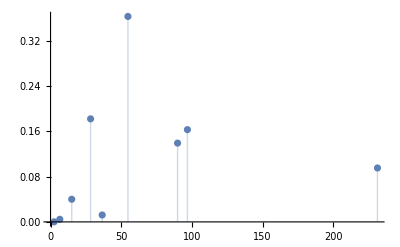

```mathematica
ListPlot[litshow[10^-4,k],Filling->Axis]
```